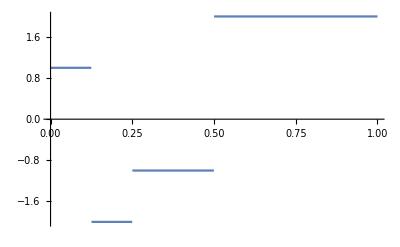

```mathematica
dyadicStep=Function[x,Piecewise[{
{1,0≤x<1/8},
{-2,1/8≤x<1/4},
{-1,1/4≤x<1/2},
{2,1/2≤x≤1}
}]];
Plot[dyadicStep[x],{x,0,1}]
```

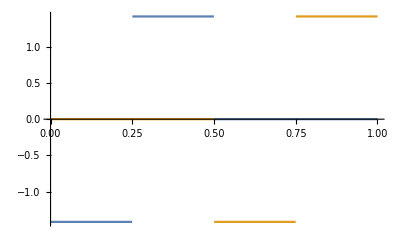

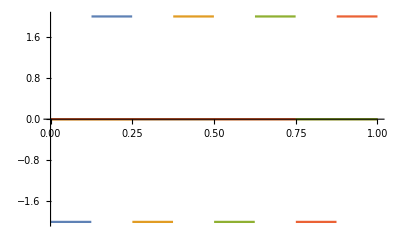

```mathematica
ϕ=Function[x,1];
ψ=Function[x,Piecewise[{
{-1,0≤x<1/2},
{1,1/2≤x≤1}
}]];
ψjk=Function[{x,j,k},2^(j/2)ψ[2^j x-k]];
Plot[{
ψjk[x,1,0],
ψjk[x,1,1]
},
{x,0,1}
]
Plot[{
ψjk[x,2,0],
ψjk[x,2,1],
ψjk[x,2,2],
ψjk[x,2,3]
},
{x,0,1}
]
```

```mathematica
(* Scaling coefficient *)
Integrate[dyadicStep[x]*ϕ[x],{x,0,1}]

(* Detail coefficients *)
Table[Table[
Integrate[dyadicStep[x]*ψjk[x,j,k],{x,0,1}],
{k,0,2^j-1}
],{j,0,3}]
```

5/8

{{11/8},{-1/(4 √2),0},{-3/4,0,0,0},{0,0,0,0,0,0,0,0}}